```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/joshuakhorsandi/Documents/Summer Research - 2023/WSS 2023/Chem Space - #225/ChemicalSpaceNetworks/ChemicalSpaceNetworks/Src

```mathematica
Needs["WolframChemistry`MoleculeFingerprints`"]
```

### generateEdges[]

```mathematica
Options[generateEdges]=Options[MoleculeDistance];
generateEdges[data_Dataset,opts:OptionsPattern[]]:=With[{mols=KeyValueMap[{#1,#2["Fingerprint"]}&,data]//Normal},
ParallelMap[UndirectedEdge[Sequence@@First/@#]->N@*OptionValue["DistanceFunction"]@@Last/@#&,Subsets[mols,{2}]]//Association]
```

### generateMatrix[]

```mathematica
Options[generateDistanceMatrix]=Options[MoleculeDistanceMatrix];
generateDistanceMatrix[data_Dataset]:=
MoleculeDistanceMatrix[Normal@Values@data[All,"Molecule"]]
```

### generateGraph[]

```mathematica
Options[generateGraph]={"Embedding"->"GravityEmbedding"};
generateGraph[edges_,cutoff_Real,OptionsPattern[]]:=
Select[edges,#<=cutoff&]//Keys//Graph[Tooltip/@Union@@List@@@#,#,GraphLayout->OptionValue["Embedding"]]&;
```

### Example: D5 Dataset

```mathematica
d5FingerPrints=Import["../Data/fingerPrintDataD5.wxf"]
```

Dataset[<>]

```mathematica
edgeData=generateEdges[d5FingerPrints]
```

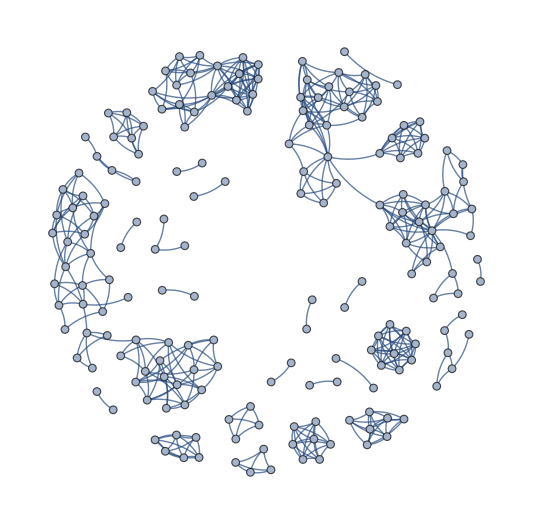

```mathematica
g=generateGraph[edgeData,0.5]
```

```mathematica
m=generateDistanceMatrix[d5FingerPrints]
```

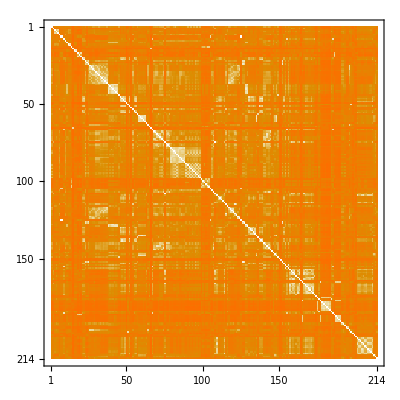

```mathematica
MatrixPlot[m]
```